## EJERCICIO 2 APARTADO C

```mathematica
(*Datos*)
q = 0.5;
lambda = 2000;
mu = 2500;
incognitas={p0,p11,p12,p2,p3,p4,p5,p6 ,p7,p8,p9,p10};
ecuaciones={
p0 +p11+p12+p2+p3+p4+p5+p6 +p7+p8+p9+p10==1,
q*lambda*p0 +(1-q)*lambda*p0 ==mu*p11+mu*p12,
lambda*p11 +mu*p11 == q*lambda*p0+mu*p2,
lambda*p12 +mu*p12 == (1-q)*lambda*p0+mu*p2,
lambda*p2 == 2*mu*p3,
lambda*p3 == 2*mu*p4,
lambda*p4 == 2*mu*p5,
lambda*p5 == 2*mu*p6,
lambda*p6 == 2*mu*p7,
lambda*p7 == 2*mu*p8,
lambda*p8 == 2*mu*p9,
lambda*p9 == 2*mu*p10
};
```

```mathematica
solucion=Solve[ecuaciones,incognitas]
p0r=p0/. solucion[[1]];
p11r=p11/. solucion[[1]];
p12r=p12/. solucion[[1]];
p2r=p2/. solucion[[1]];
p3r=p3/. solucion[[1]];
p4r=p4/. solucion[[1]];
p5r=p5/. solucion[[1]];
p6r=p6/. solucion[[1]];
p7r=p7/. solucion[[1]];
p8r=p8/. solucion[[1]];
p9r=p9/. solucion[[1]];
p10r=p10/. solucion[[1]];
```

{{p0→0.428597,p11→0.171439,p12→0.171439,p2→0.137151,p3→0.0548604,p4→0.0219442,p5→0.00877767,p6→0.00351107,p7→0.00140443,p8→0.000561771,p9→0.000224708,p10→0.0000898833}}

```mathematica
0.00008988332854292062
```

0.0000898833

```mathematica
Th = mu*(p11r+p12r) + 2*mu (p2r+p3r+p4r+ p5r+p6r +p7r+p8r+p9r+p10r)
```

1999.82

```mathematica
valoresPr={p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r};

En =∑_(n=0)^10 n*valoresPr[[n+1]]
```

1.35071

```mathematica
calcularTh[lambda_, mu_,q_]:=Module[{p0,p11,p12,p2,p3,p4,p5,p6,p7,p8,p9,p10, p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r},
incognitas={p0,p11,p12,p2,p3,p4,p5,p6 ,p7,p8,p9,p10};
ecuaciones={
p0 +p11+p12+p2+p3+p4+p5+p6 +p7+p8+p9+p10==1,
q*lambda*p0 +(1-q)*lambda*p0 ==mu*p11+mu*p12,
lambda*p11 +mu*p11 == q*lambda*p0+mu*p2,
lambda*p12 +mu*p12 == (1-q)*lambda*p0+mu*p2,
lambda*p2 == 2*mu*p3,
lambda*p3 == 2*mu*p4,
lambda*p4 == 2*mu*p5,
lambda*p5 == 2*mu*p6,
lambda*p6 == 2*mu*p7,
lambda*p7 == 2*mu*p8,
lambda*p8 == 2*mu*p9,
lambda*p9 == 2*mu*p10
};

solucion=Solve[ecuaciones,incognitas];
p0r=p0/. solucion[[1]];
p11r=p11/. solucion[[1]];
p12r=p12/. solucion[[1]];
p2r=p2/. solucion[[1]];
p3r=p3/. solucion[[1]];
p4r=p4/. solucion[[1]];
p5r=p5/. solucion[[1]];
p6r=p6/. solucion[[1]];
p7r=p7/. solucion[[1]];
p8r=p8/. solucion[[1]];
p9r=p9/. solucion[[1]];
p10r=p10/. solucion[[1]];

Th = mu*(p11r+p12r) + 2*mu (p2r+p3r+p4r+ p5r+p6r +p7r+p8r+p9r+p10r)
]
```

```mathematica
calcularEt[lambda_, mu_,q_]:=Module[{p0,p11,p12,p2,p3,p4,p5,p6,p7,p8,p9,p10, p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r},
incognitas={p0,p11,p12,p2,p3,p4,p5,p6 ,p7,p8,p9,p10};
ecuaciones={
p0 +p11+p12+p2+p3+p4+p5+p6 +p7+p8+p9+p10==1,
q*lambda*p0 +(1-q)*lambda*p0 ==mu*p11+mu*p12,
lambda*p11 +mu*p11 == q*lambda*p0+mu*p2,
lambda*p12 +mu*p12 == (1-q)*lambda*p0+mu*p2,
lambda*p2 == 2*mu*p3,
lambda*p3 == 2*mu*p4,
lambda*p4 == 2*mu*p5,
lambda*p5 == 2*mu*p6,
lambda*p6 == 2*mu*p7,
lambda*p7 == 2*mu*p8,
lambda*p8 == 2*mu*p9,
lambda*p9 == 2*mu*p10
};

solucion=Solve[ecuaciones,incognitas];
p0r=p0/. solucion[[1]];
p11r=p11/. solucion[[1]];
p12r=p12/. solucion[[1]];
p2r=p2/. solucion[[1]];
p3r=p3/. solucion[[1]];
p4r=p4/. solucion[[1]];
p5r=p5/. solucion[[1]];
p6r=p6/. solucion[[1]];
p7r=p7/. solucion[[1]];
p8r=p8/. solucion[[1]];
p9r=p9/. solucion[[1]];
p10r=p10/. solucion[[1]];
valoresPr={p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r};
En =∑_(n=0)^10 n*valoresPr[[n+1]]
]
```

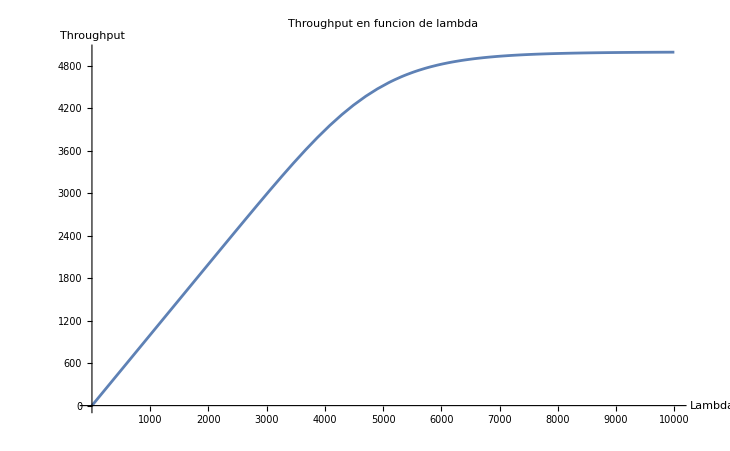

```mathematica
Plot[calcularTh[lambda,mu,q],{lambda, 0,10000}, Ticks->{Range[1000,10000,1000],Automatic},PlotLabel->"Throughput en funcion de lambda",AxesLabel->{"Lambda","Throughput"},PlotRange->All]
```

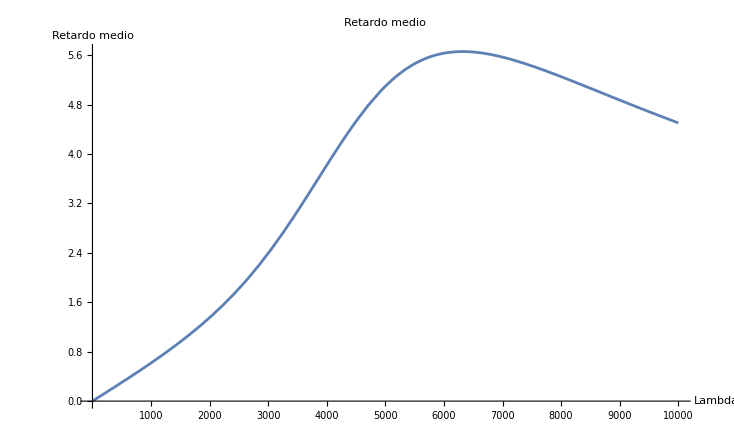

```mathematica
Plot[calcularEt[lambda,mu,q],{lambda, 0,10000}, Ticks->{Range[1000,10000,1000],Automatic},PlotLabel->"Retardo medio",AxesLabel->{"Lambda","Retardo medio"},PlotRange->All]
```

## EJERCICIO 2 APARTADO D

```mathematica
q = 0.5;
lambda = 2000;
mu = 2500;
incognitas={p0,p11,p12,p2,p3,p4,p5,p6 ,p7,p8,p9,p10};
ecuaciones={
p0 +p11+p12+p2+p3+p4+p5+p6 +p7+p8+p9+p10==1,
q*lambda*p0 +(1-q)*lambda*p0 ==4*mu*p11+mu*p12,
lambda*p11 +4*mu*p11 == q*lambda*p0+mu*p2,
lambda*p12 +mu*p12 == (1-q)*lambda*p0+4*mu*p2,

lambda*p2 == 5*mu*p3,
lambda*p3 == 5*mu*p4,
lambda*p4 == 5*mu*p5,
lambda*p5 == 5*mu*p6,
lambda*p6 == 5*mu*p7,
lambda*p7 == 5*mu*p8,
lambda*p8 == 5*mu*p9,
lambda*p9 == 5*mu*p10
};
```

```mathematica
solucion=Solve[ecuaciones,incognitas]
```

{{p0→0.626866,p11→0.0626866,p12→0.250746,p2→0.0501493,p3→0.00802388,p4→0.00128382,p5→0.000205411,p6→0.0000328658,p7→5.25853×10^-6,p8→8.41365×10^-7,p9→1.34618×10^-7,p10→2.15389×10^-8}}

```mathematica
Th = mu*(p11r+p12r) + 2*mu (p2r+p3r+p4r+ p5r+p6r +p7r+p8r+p9r+p10r)
valoresPr={p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r};

En =∑_(n=0)^10 n*valoresPr[[n+1]]
```

1999.82

1.35071

```mathematica
calcularTh2[lambda_, mu_,q_]:=Module[{p0,p11,p12,p2,p3,p4,p5,p6,p7,p8,p9,p10, p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r},
incognitas={p0,p11,p12,p2,p3,p4,p5,p6 ,p7,p8,p9,p10};
ecuaciones={
p0 +p11+p12+p2+p3+p4+p5+p6 +p7+p8+p9+p10==1,
q*lambda*p0 +(1-q)*lambda*p0 ==4*mu*p11+mu*p12,
lambda*p11 +4*mu*p11 == q*lambda*p0+mu*p2,
lambda*p12 +mu*p12 == (1-q)*lambda*p0+4*mu*p2,

lambda*p2 == 5*mu*p3,
lambda*p3 == 5*mu*p4,
lambda*p4 == 5*mu*p5,
lambda*p5 == 5*mu*p6,
lambda*p6 == 5*mu*p7,
lambda*p7 == 5*mu*p8,
lambda*p8 == 5*mu*p9,
lambda*p9 == 5*mu*p10
};
solucion=Solve[ecuaciones,incognitas];
p0r=p0/. solucion[[1]];
p11r=p11/. solucion[[1]];
p12r=p12/. solucion[[1]];
p2r=p2/. solucion[[1]];
p3r=p3/. solucion[[1]];
p4r=p4/. solucion[[1]];
p5r=p5/. solucion[[1]];
p6r=p6/. solucion[[1]];
p7r=p7/. solucion[[1]];
p8r=p8/. solucion[[1]];
p9r=p9/. solucion[[1]];
p10r=p10/. solucion[[1]];

Th = mu*(p11r+p12r) + 2*mu (p2r+p3r+p4r+ p5r+p6r +p7r+p8r+p9r+p10r)
]
```

```mathematica
calcularEt2[lambda_, mu_,q_]:=Module[{p0,p11,p12,p2,p3,p4,p5,p6,p7,p8,p9,p10, p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r},
incognitas={p0,p11,p12,p2,p3,p4,p5,p6 ,p7,p8,p9,p10};
ecuaciones={
p0 +p11+p12+p2+p3+p4+p5+p6 +p7+p8+p9+p10==1,
q*lambda*p0 +(1-q)*lambda*p0 ==4*mu*p11+mu*p12,
lambda*p11 +4*mu*p11 == q*lambda*p0+mu*p2,
lambda*p12 +mu*p12 == (1-q)*lambda*p0+4*mu*p2,

lambda*p2 == 5*mu*p3,
lambda*p3 == 5*mu*p4,
lambda*p4 == 5*mu*p5,
lambda*p5 == 5*mu*p6,
lambda*p6 == 5*mu*p7,
lambda*p7 == 5*mu*p8,
lambda*p8 == 5*mu*p9,
lambda*p9 == 5*mu*p10
};
solucion=Solve[ecuaciones,incognitas];
p0r=p0/. solucion[[1]];
p11r=p11/. solucion[[1]];
p12r=p12/. solucion[[1]];
p2r=p2/. solucion[[1]];
p3r=p3/. solucion[[1]];
p4r=p4/. solucion[[1]];
p5r=p5/. solucion[[1]];
p6r=p6/. solucion[[1]];
p7r=p7/. solucion[[1]];
p8r=p8/. solucion[[1]];
p9r=p9/. solucion[[1]];
p10r=p10/. solucion[[1]];

valoresPr={p0r,p11r,p12r,p2r,p3r,p4r,p5r,p6r,p7r,p8r,p9r,p10r};
En =∑_(n=0)^10 n*valoresPr[[n+1]]]
```

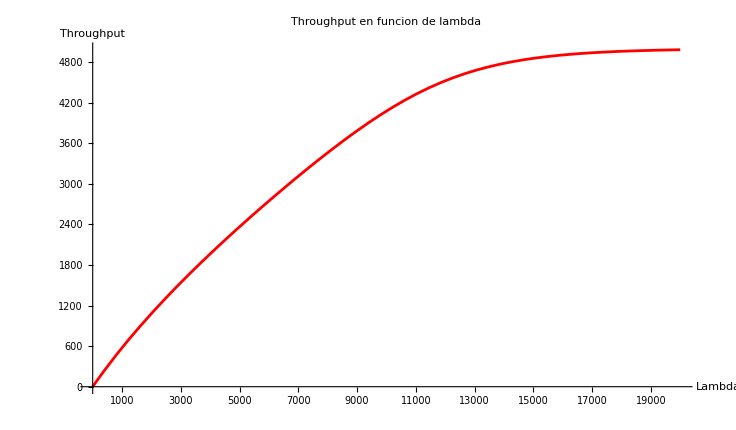

```mathematica
Plot[calcularTh2[lambda,mu,q],{lambda, 0,20000}, Ticks->{Range[1000,20000,2000],Automatic},PlotLabel->"Throughput en funcion de lambda",AxesLabel->{"Lambda","Throughput"},PlotRange->All, PlotStyle->Red]
```

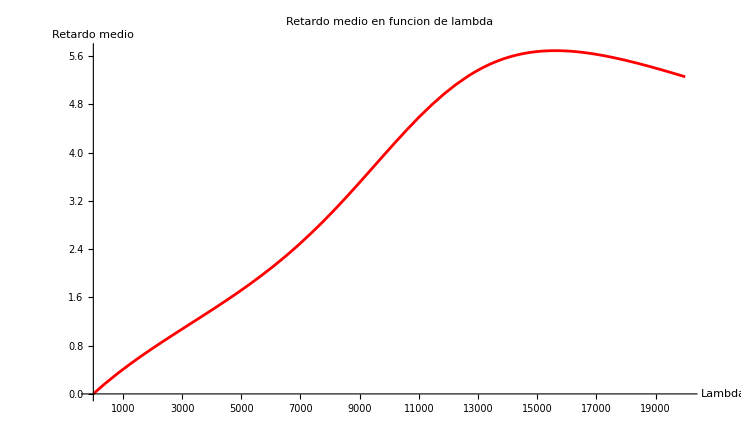

```mathematica
Plot[calcularEt2[lambda,mu,q],{lambda, 0,20000}, Ticks->{Range[1000,20000,2000],Automatic},PlotLabel->"Retardo medio en funcion de lambda",AxesLabel->{"Lambda","Retardo medio"},PlotStyle->Red]
```

## Comparaciones

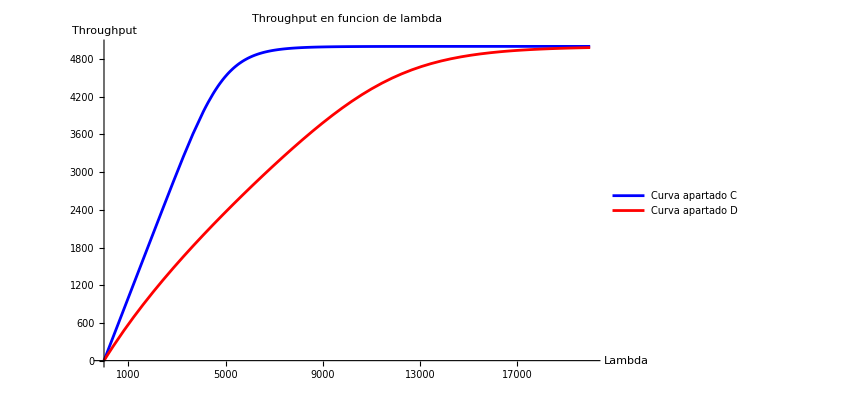

```mathematica
Show[
Plot[calcularTh[lambda,mu,q],{lambda, 0,20000}, Ticks->{Range[1000,20000,2000],Automatic},PlotLabel->"Throughput en funcion de lambda",AxesLabel->{"Lambda","Throughput"},PlotRange->All, PlotLegends->{"Curva apartado C"}, PlotStyle->Blue],
Plot[calcularTh2[lambda,mu,q],{lambda, 0,20000}, Ticks->{Range[1000,20000,2000],Automatic},PlotLabel->"Throughput en funcion de lambda",AxesLabel->{"Lambda","Throughput"},PlotRange->All, PlotLegends->{"Curva apartado D"}, PlotStyle->Red]
]
```

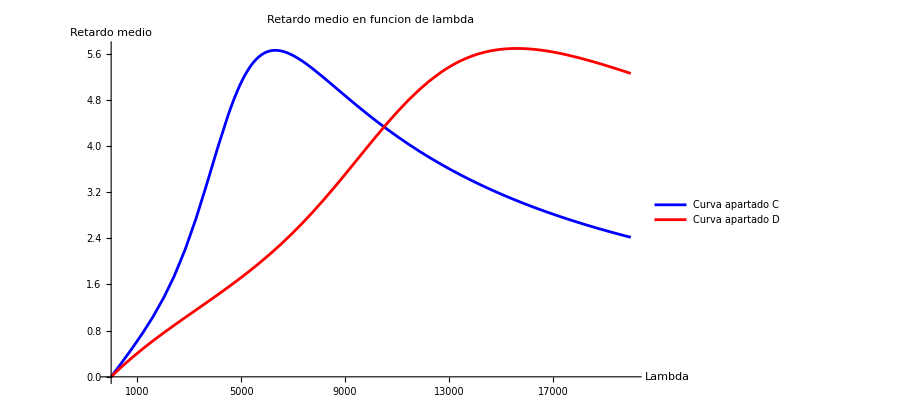

```mathematica
Show[
Plot[calcularEt[lambda,mu,q],{lambda, 0,20000}, Ticks->{Range[1000,20000,2000],Automatic},PlotLabel->"Retardo medio en funcion de lambda",AxesLabel->{"Lambda","Retardo medio"},PlotRange->All, PlotLegends->{"Curva apartado C"}, PlotStyle->Blue],
Plot[calcularEt2[lambda,mu,q],{lambda, 0,20000}, Ticks->{Range[1000,20000,2000],Automatic},PlotLabel->"Retardo medio en funcion de lambda",AxesLabel->{"Lambda","Retardo medio"},PlotRange->All, PlotLegends->{"Curva apartado D"}, PlotStyle->Red]
]
```